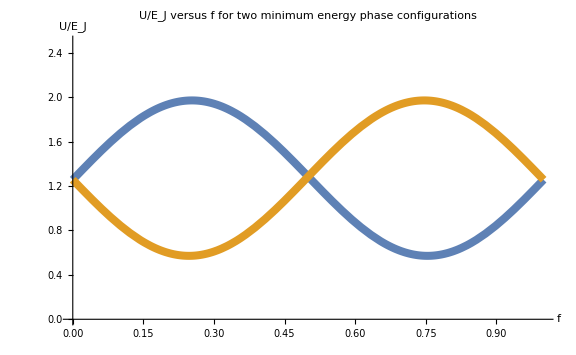

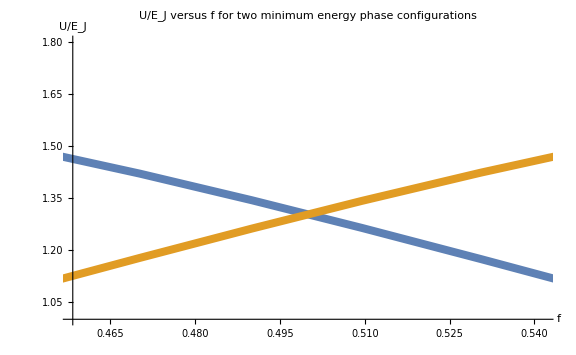

```mathematica
α=0.7;
U1[f_]:=2+α-2Cos[ϕ]-α Cos[2π*f+2ϕ];
Plot[{U1[f]/.ϕ->ArcCos[1/(2*α)],U1[f]/.ϕ->-ArcCos[1/(2*α)]} ,{f,0,1},
PlotStyle->{Directive[Thickness[0.01]]},  AxesLabel->{Style["f",16],Style["U/"<>ToString[Subscript["E",J],StandardForm],16]},
PlotLabel->Style["U/"<>ToString[Subscript["E",J],StandardForm]"versus f for two minimum energy phase configurations", Black, FontSize->20], 
ImageSize->Large, PlotRange->{{0,1},{0,2.5}}  ] (* , GridLines->{{0.5},{0.2,2+α-2Cos[ArcCos[1/(2*0.7)]]}} *)

fc[α_]:=(1/(2π))*(2 ArcCos[2 Sqrt[(1-α^2)/3]]-ArcCos[Sqrt[(1-α^2)/(3α^2)]]);
Plot[{U1[f]/.ϕ->ArcCos[2 Sqrt[(1-α^2)/3]], U1[f]/.ϕ->-ArcCos[2 Sqrt[(1-α^2)/3]]} ,{f,0,1},
PlotStyle->{Directive[Thickness[0.01]]},  AxesLabel->{Style["f",16],Style["U/"<>ToString[Subscript["E",J],StandardForm],16]},
PlotLabel->Style["U/"<>ToString[Subscript["E",J],StandardForm]"versus f for two minimum energy phase configurations", Black, FontSize->20], 
ImageSize->Large, PlotRange->{{0.5-fc[α],0.5+fc[α]},{1,1.8}}]
```

```mathematica
fc[0.7]
```

0.0416304